```mathematica
Needs["Notation`"];
```

```mathematica
Needs["MaTeX`"];
```

```mathematica
(*$RecursionLimit=100*)
```

```mathematica
(*p1 = {p10,p11,p12,p13};
p2 = {p20,p21,p22,p23};
q = {q0,q1,q2,q3};
l = {l0, l1,l2, l3};
b = {b0, b1,b2,b3};
Q = {Q0,Q1,Q2,Q3};*)
```

```mathematica
(*eta = DiagonalMatrix[{1,-1,-1,-1}];*)
```

```mathematica
(*ClearAll[p1,p2,q,l,b, Q, eta];
vecRules = {p1 -> {p10,p11,p12,p13},
p2 -> {p20,p21,p22,p23},
q -> {q0,q1,q2,q3},
l -> {l0, l1,l2, l3},
b -> {b0, b1,b2,b3},
(*Q -> {Q0,Q1,Q2,Q3},*)
Qp -> {Qp0, Qp1, Qp2, Qp3},
eta -> DiagonalMatrix[{1,-1,-1,-1}]};*)
```

```mathematica
(*RealQ[num_] := TrueQ[Refine[Element[num, Reals]]];
IsReal[x_] := FreeQ[RealQ[x],x∈Reals];*)
```

```mathematica
(*scalars = {x1, x2, m1, m2, S};
IsScalar[x_]:=MemberQ[scalars, x]||NumberQ[x]*)
```

```mathematica
ClearAll[scalars];
scalars={x1,x2,m1,m2,S,ℏ,ρ,γ,ϵ};

$Assumptions=And@@(Element[#,Reals]&/@scalars);

IsScalar[expr_]:=Module[{vars, dotExp},
vars = Variables[expr];
dotExp = Cases[vars,holdDot[_,_]];
vars=Complement[vars,dotExp];
vars =Join[vars,HoldForm/@dotExp];

(vars==={}&&NumericQ[expr])||(vars=!={}&&SubsetQ[scalars,vars])
];

(*IsScalar[expr_]:=Module[{vars},
vars=Variables[expr];

(vars==={}&&NumericQ[expr])||(vars=!={}&&SubsetQ[scalars,vars])
];*)
```

```mathematica
scalars
```

{x1,x2,m1,m2,S,ℏ,ρ,γ,ϵ}

```mathematica
AddToScalars[expr_]:=(If[!MemberQ[scalars,HoldForm[expr]],scalars=Append[scalars,HoldForm[expr]]];
expr);

AddDotProdToScalars[vectors_]:=Module[{vecPairs},
(*vecPairs = Subsets[vectors,{2}];*)
vecPairs=DeleteDuplicatesBy[Tuples[vectors,2], Sort];
dotProdPairs = holdDot@@#&/@ vecPairs;
Do[AddToScalars[dotProd], {dotProd, dotProdPairs}];
];
```

```mathematica
holdDotDef:=(
ClearAll[holdDot];(*holdDot[a_,b_]:=Module[{aa=a,bb=b},If[OrderedQ[{aa,bb}],a.eta.b,b.eta.a]];*)
(*holdDot/:holdDot[a_,b_]:=If[OrderedQ[{a,b}],holdDot[a,b],holdDot[b,a]];*)
(*holdDot/:holdDot[a_,b_]:=0/;(PossibleZeroQ[a]||PossibleZeroQ[b]);
holdDot/:holdDot[a_,b_]:=holdDot@@Sort[{a,b}]/;!OrderedQ[{a,b}];*)
holdDot[a_,b_]:=0/;(PossibleZeroQ[a]||PossibleZeroQ[b]);
holdDot[a_,b_]:=holdDot@@Sort[{a,b}]/;!OrderedQ[{a,b}];
holdDot[a_+b_, x_]:=holdDot[a,x]+holdDot[b,x];
holdDot[x_, a_+b_]:=holdDot[a,x]+holdDot[b,x];
holdDot[x_,c_?IsScalar y_]:= c holdDot[x,y];
holdDot[c_?IsScalar x_, y_]:= c holdDot[x,y];
holdDot[x_, Times[holdDot[a_,b_], y_]]:= holdDot[a,b]×holdDot[x,y];
holdDot[Times[holdDot[a_,b_]x_], y_]:= holdDot[a,b]× holdDot[x,y];
(*holdDot[c_ x_,y_]:=c holdDot[x,y]/;FreeQ[c,_List];
holdDot[x_,c_ y_]:=c holdDot[x,y]/;FreeQ[c,_List];*)


Notation[ParsedBoxWrapper[RowBox[{"a_","⊙","b_"}]]⇔ParsedBoxWrapper[RowBox[{"holdDot","[","a_",",","b_","]"}]]];
)
```

```mathematica
holdDotDer:=(
(*ClearAll[holdDot];*)

SetOptions[D,NonConstants->{holdDot, Wedge}];
(*D[expr_holdDot,vars__]^:=Module[{x,y,z},*)
holdDot/:D[holdDot[a_,b_],vars__]:=Module[{x=a,y=b,z},
(*{x,y}=List@@expr;*)
z={vars}[[1]];
Which[
IsScalar[z]&&x===q&&y===q,
holdDot[D[Q,{vars}[[1]]],y]+holdDot[x,D[Q,{vars}[[1]]]],
IsScalar[z]&&x===q,
holdDot[D[Q,{vars}[[1]]],y],
IsScalar[z]&&y===q,
holdDot[x,D[Q,{vars}[[1]]]],
!IsScalar[{vars}[[1]]],
x×D[y,{vars}[[1]]]+y×D[x,{vars}[[1]]],
True,0]];
)
```

```mathematica
holdDotDef
```

Notation::oldnota: Future versions of the Notation package will no longer support ⇔, instead they will use ⟺. Please make this change to all your Notations.

```mathematica
vectors={p1,p2,q,l, Qp}
```

{p1,p2,q,l,Qp}

```mathematica
AddDotProdToScalars[vectors]
```

```mathematica
scalars
```

{x1,x2,m1,m2,S,ℏ,ρ,γ,ϵ,p1⊙p1,p1⊙p2,p1⊙q,l⊙p1,p1⊙Qp,p2⊙p2,p2⊙q,l⊙p2,p2⊙Qp,q⊙q,l⊙q,q⊙Qp,l⊙l,l⊙Qp,Qp⊙Qp}

```mathematica
ClearAll[Wedge];

Wedge[x_,y_]:=0/;(x===y||PossibleZeroQ[x]||PossibleZeroQ[y]);
Wedge[a_+b_, x_]:=Wedge[a,x]+Wedge[b,x];
Wedge[x_, a_+b_]:=Wedge[x,a]+Wedge[x,b];
Wedge[x_,c_?IsScalar y_]:= c Wedge[x,y];
Wedge[c_?IsScalar x_, y_]:= c Wedge[x,y];
Wedge[x_,y_]:=-Wedge[y,x]/;OrderedQ[{y,x}];
Wedge[x_, Times[holdDot[a_,b_], y_]]:= holdDot[a,b]×Wedge[x,y];
Wedge[Times[holdDot[a_,b_]x_], y_]:= holdDot[a,b]× Wedge[x,y];
```

```mathematica
wedgeDer:=(SetOptions[D,NonConstants->{holdDot, Wedge}];
(*D[expr_Wedge,vars__]^:=Module[{x,y,z},*)
Wedge/:D[Wedge[a_,b_],vars__]:=Module[{x=a,y=b,z},
(*{x,y}=List@@expr;*)
z={vars}[[1]];
Which[
IsScalar[z]&&x===q&&y===q,
Wedge[D[Q,{vars}[[1]]],y]+Wedge[x,D[Q,{vars}[[1]]]],
IsScalar[z]&&x===q,
Wedge[D[Q,{vars}[[1]]],y],
IsScalar[z]&&y===q,
Wedge[x,D[Q,{vars}[[1]]]],
!IsScalar[{vars}[[1]]],
Wedge[x,D[y,{vars}[[1]]]]+Wedge[D[x,{vars}[[1]]],y],
True,0]];

)
```

```mathematica
wedgeDer
```

```mathematica
D[Wedge[p2,q]/holdDot[p1,q],x2]
```

0

```mathematica
Wedge[p1,p2/(p1⊙p2)^2]
```

(p1⋀p2)/(p1⊙p2)^2

```mathematica
aWedgeDb[expr_, a_,b_]:= Wedge[a,D[expr,b]];
aWedgeDb[expr_holdDot, a_,b_]:= Module[{x,y}, {x,y}=List@@expr;
Wedge[a,y D[x,b]]+Wedge[a,x D[y,b]]];
```

```mathematica
(*ClearAll[holdDot]*)
(*SetAttributes[holdDot,HoldAll]*)
```

```mathematica
(*holdDot[a_,b_]:=Module[{aa=a,bb=b},If[OrderedQ[{aa,bb}],HoldForm[a.eta.b],HoldForm[b.eta.a]]];*)
(*holdDot[a_,b_]:=Module[{aa=a,bb=b},If[OrderedQ[{aa,bb}],a.eta.b,b.eta.a]];
holdDot[a_+b_, x_]:=holdDot[a,x]+holdDot[b,x];
holdDot[x_, a_+b_]:=holdDot[a,x]+holdDot[b,x];
holdDot[x_, c_?NumberQ y_]:= c holdDot[x,y];
holdDot[c_?NumberQ x_, y_]:= c holdDot[x,y];
holdDot[c_ x_,y_]:=c holdDot[x,y]/;FreeQ[c,_List];
holdDot[x_,c_ y_]:=c holdDot[x,y]/;FreeQ[c,_List];*)
```

```mathematica
(*UpValues[holdDot]={};
holdDot,Dt[holdDot[x_,y_], z,___]:=Which[
x===q&&y===q,
 holdDot[D[Q, z],y]+holdDot[x,D[Q, z]],
x===q,
holdDot[D[Q,z],y],
y===q,
holdDot[x,D[Q, z]],
True,
 0 ]*)

(*holdDot/:D[holdDot[x_,y_],z_,NonConstants->_]:=D[holdDot[x,y],z]*)
```

```mathematica
(*wrapDot[expr_ ] :=expr //.{(p1.eta.p1/.vecRules)->Subscript[m, 1]^2,(-p1.eta.p1/.vecRules)->-Subscript[m, 1]^2,(p2.eta.p2/.vecRules)->Subscript[m, 2]^2,(-p2.eta.p2/.vecRules)->-Subscript[m, 2]^2,
(p1.eta.p2/.vecRules)->γ,(-p1.eta.p2/.vecRules)->-γ,(p1.eta.q/.vecRules)->p1.eta.q,(-p1.eta.q/.vecRules)->-p1.eta.q,(p2.eta.q/.vecRules)->p2.eta.q,(-p2.eta.q/.vecRules)->-p2.eta.q,(p1.eta.l/.vecRules)->p1.eta.l,(-p1.eta.l/.vecRules)->-p1.eta.l,(p2.eta.l/.vecRules)->p2.eta.l,(-p2.eta.l/.vecRules)->-p2.eta.l,(l.eta.q/.vecRules)->l.eta.q,(-l.eta.q/.vecRules)->-l.eta.q,
(l.eta.l/.vecRules)->l.eta.l,(-l.eta.l/.vecRules)->-l.eta.l,
(q.eta.q/.vecRules)->q.eta.q,(-q.eta.q/.vecRules)->-q.eta.q}*)
```

```mathematica
(*holdDot[a_, b_]:=a.eta.b//FullSimplify//.{p1.eta.p2->HoldForm[HoldPattern[γ],-p1.eta.p2->-HoldForm[γ],p1.eta.q->HoldForm[p1.eta.q],-p1.eta.q->-HoldForm[p1.eta.q],p2.eta.q->HoldForm[p2.eta.q],-p2.eta.q->-HoldForm[p2.eta.q],p1.eta.l->HoldForm[p1.eta.l],-p1.eta.l->-HoldForm[p1.eta.l],p2.eta.l->HoldForm[p2.eta.l],-p2.eta.l->-HoldForm[p2.eta.l],l.eta.q->HoldForm[l.eta.q],-l.eta.q->-HoldForm[l.eta.q]}*)
```

```mathematica
(*wrapDot[expr_, ] :=expr //.{p1.eta.p2->HoldForm[γ],-p1.eta.p2->-HoldForm[γ],p1.eta.q->HoldForm[p1.eta.q],-p1.eta.q->-HoldForm[p1.eta.q],p2.eta.q->HoldForm[p2.eta.q],-p2.eta.q->-HoldForm[p2.eta.q],p1.eta.l->HoldForm[p1.eta.l],-p1.eta.l->-HoldForm[p1.eta.l],p2.eta.l->HoldForm[p2.eta.l],-p2.eta.l->-HoldForm[p2.eta.l],l.eta.q->HoldForm[l.eta.q],-l.eta.q->-HoldForm[l.eta.q],
l.eta.l->HoldForm[l.eta.l],-l.eta.l->-HoldForm[l.eta.l],
q.eta.q->HoldForm[q.eta.q],-q.eta.q->-HoldForm[q.eta.q]}*)
```

```mathematica
(*holdDot[expr_] :=Simplify[expr ,{p1.eta.p2->HoldForm[γ],p1.eta.q->HoldForm[p1.eta.q],p2.eta.q->HoldForm[p2.eta.q],p1.eta.l->HoldForm[p1.eta.l],p2.eta.l->HoldForm[p2.eta.l],l.eta.q->HoldForm[l.eta.q]}]*)
```

```mathematica
holdDotDef
```

Notation::oldnota: Future versions of the Notation package will no longer support ⇔, instead they will use ⟺. Please make this change to all your Notations.

```mathematica
α1= (γ x2-m2^2 x1)/S;
α2 = (γ x1-m1^2 x2)/S;
Q = α1 p1+α2 p2+Qp;
q == Q;
```

```mathematica
holdDotDer
```

```mathematica
wedgeDer
```

```mathematica
D[holdDot[p1,q]/holdDot[p2,q],x1]
```

-(p1⊙q (-(m2^2 p1⊙p2)/S+(γ p2⊙p2)/S))/(p2⊙q)^2+(-(m2^2 p1⊙p1)/S+(γ p1⊙p2)/S)/(p2⊙q)

```mathematica
onShellP[expr_]:=expr//.{p1⊙q->0, p2⊙q->0,p1⊙p2->γ, p1⊙p1->m1^2,p2⊙p2->m2^2}
(*onShellP[expr_]:=expr//.{HoldForm[p1.eta.q]->0, HoldForm[p2.eta.q]->0}*)
```

```mathematica
simplifiedForm[expr_]:=expr/.{(-(m1^2 m2^2)/S+γ^2/S)->1,((m1^2 m2^2)/S-γ^2/S)->-1}//.{(coef1_. ϵ+coef2_. l1dot_+rest_.)^(n_.):>(coef2)^n*(ϵ*(coef1/coef2)/Abs[coef1/coef2]+l1dot+Distribute[rest/coef2])^n/;l1dot==l⊙p1||l1dot==l⊙p2||l1dot==l1⊙p1||l1dot==l1⊙p2||l1dot==l2⊙p1||l1dot==l2⊙p2}
```

```mathematica
cancelFactors[expr_]:=expr//.{ dot1:d1_^(n_.)*(c1_. ϵ+ dot2:d2_+d3___)^(m_)/;d1==d2+d3->If[Abs[n]<Abs[m],(c1 ϵ+ d1)^(m+n),d1^(m+n)]}
```

```mathematica
factorRho[exp_]:=exp/.{(expr_Plus)^(n_):>Factor[expr]^n/;ContainsAll[Variables[expr], {ϵ,l⊙p1}]||ContainsAll[Variables[expr], {ϵ,l⊙p2}]}
```

```mathematica
simplifyTerm[expr_]:=expr//.{(num_ a_)/(Power[den_,-n_]):>num/(den^(-n-1))/;ContainsAll[Variables[den],{ϵ,a}]/;a==l⊙p1||a==l⊙p2}
```

```mathematica
cancelFactors[expr_]:=expr//.{ dot1:d1_^(n_.)*(c1_. ϵ+ dot2:d2_+d3___)^(m_)/;d1==d2+d3->If[Abs[n]<Abs[m],(c1 ϵ+ d1)^(m+n),d1^(m+n)]}
```

```mathematica
supressQml[expr_]:=expr/.{-l1⊙l1+2 l1⊙l2+2 l1⊙q-l2⊙l2+2 l2⊙q-q⊙q->-qml1ml2,l1⊙l1+2 l1⊙l2-2 l1⊙q+l2⊙l2-2 l2⊙q+q⊙q->qml1ml2};
```

```mathematica
modifyNum[expr_]:=expr//.{(dot1_/;MemberQ[{l1⊙p1,l1⊙p2,l2⊙p1,l2⊙p2},dot1])^(n_.)*(c1_ ϵ+dot2:d1_+d2___)^(m_.)/;dot1==d1:>Expand[Hold[dot1+d2]-d2]^n*(c1 ϵ+d1+d2)^m}
```

```mathematica
(*ClearAll[holdDot]
SetOptions[D, NonConstants->{holdDot}];*)
```

```mathematica
(*Product rule when holdDot is inside product*)
(*holdDot/:D[expr_Times,z_]/;MemberQ[expr,_holdDot,{0,Infinity}]:=Module[{factors=List@@expr},Total[Table[D[factors[[i]],z]*Times@@Delete[factors,i],{i,Length[factors]}]]];*)
```

```mathematica
holdDotDef
```

Notation::oldnota: Future versions of the Notation package will no longer support ⇔, instead they will use ⟺. Please make this change to all your Notations.

```mathematica
holdDotDer
```

Notation::oldnota: Future versions of the Notation package will no longer support ⇔, instead they will use ⟺. Please make this change to all your Notations.

```mathematica
a=D[p1⊙q, x1]
b=D[p1⊙q, x2]
```

-(m2^2 p1⊙p1)/S+(γ p1⊙p2)/S

(γ p1⊙p1)/S-(m1^2 p1⊙p2)/S

## First Pair

```mathematica
Bx1 = ((2p1+ℏ l)⊙(2p2-ℏ l)(2p1+ℏ q+ℏ l)⊙(2p2-ℏ q-ℏ l))/((q-l)⊙(q-l)(2p1⊙l+ℏ l⊙l+ⅈ ϵ)(2p2⊙l-ℏ l⊙l-ⅈ ϵ));
Cx1 = ((2p1+ℏ q+ℏ l)⊙(2p2-ℏ q+ℏ l)(2p1+ℏ l)⊙(2p2-2ℏ q+ℏ l))/((q-l)⊙(q-l)(2p1⊙l+ℏ l⊙l+ⅈ ϵ)(2p2⊙(q-l)-ℏ(q-l)⊙(q-l)-ⅈ ϵ));
```

```mathematica
B1C1 = Bx1+Cx1/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2};
```

```mathematica
B1C1
```

((ℏ^2 l⊙l+2 ℏ l⊙p1+2 ℏ l⊙p2-2 ℏ^2 l⊙q+4 p1⊙p2-4 ℏ p1⊙q) (ℏ^2 l⊙l+2 ℏ l⊙p1+2 ℏ l⊙p2+4 p1⊙p2-2 ℏ p1⊙q+2 ℏ p2⊙q-ℏ^2 q⊙q))/(qml2 (ⅈ ϵ+ℏ l⊙l+2 l⊙p1) (-ⅈ ϵ-qml2 ℏ+2 (-l⊙p2+p2⊙q)))+((-ℏ^2 l⊙l-2 ℏ l⊙p1+2 ℏ l⊙p2+4 p1⊙p2) (-ℏ^2 l⊙l-2 ℏ l⊙p1+2 ℏ l⊙p2-2 ℏ^2 l⊙q+4 p1⊙p2-2 ℏ p1⊙q+2 ℏ p2⊙q-ℏ^2 q⊙q))/(qml2 (ⅈ ϵ+ℏ l⊙l+2 l⊙p1) (-ⅈ ϵ-ℏ l⊙l+2 l⊙p2))

```mathematica
Do[Bx1hbar[n] = Coefficient[Normal[Series[Bx1, {ℏ,0,1}]],ℏ,n];
Cx1hbar[n] = Coefficient[Normal[Series[Cx1, {ℏ,0,1}]],ℏ,n],{n,0,1}];
```

```mathematica
simplifiedForm@Bx1hbar[1]
```

1/(l⊙l-2 l⊙q+q⊙q)(4 p1⊙p2 ((-2 l⊙p1+2 l⊙p2)/(4 (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+4 ((l⊙l)/(8 (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2)^2)-(l⊙l)/(8 (ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))) p1⊙p2)-(2 p1⊙p2 (l⊙p1-l⊙p2+p1⊙q-p2⊙q))/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2)))

```mathematica
simplifiedForm@Cx1hbar[1]
```

((4 p1⊙p2 (-(l⊙l p1⊙p2)/(ⅈ ϵ+l⊙p1)^2+(l⊙p1+l⊙p2-2 p1⊙q)/(ⅈ ϵ+l⊙p1))+(4 p1⊙p2 (l⊙p1+l⊙p2-p1⊙q+p2⊙q))/(ⅈ ϵ+l⊙p1))/(-2 ⅈ ϵ-2 l⊙p2+2 p2⊙q)+(8 (p1⊙p2)^2 (-l⊙l+2 l⊙q-q⊙q))/((ⅈ ϵ+l⊙p1) (2 ϵ-2 ⅈ l⊙p2+2 ⅈ p2⊙q)^2))/(l⊙l-2 l⊙q+q⊙q)

### R_2

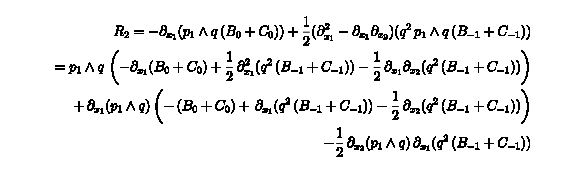

```mathematica
MaTeX["\\begin{aligned}R_2 = -\\partial_{x_1}(p_1\\wedge q\\,(B_0+C_0))+\\frac{1}{2}(\\partial_{x_1}^2-\\partial_{x_1}\\partial_{x_2})(q^2\\,p_1\\wedge q\\,(B_{-1}+C_{-1}))\\\\=p_1\\wedge q\\,\\left(-\\partial_{x_1}(B_0+C_0)+\\frac{1}{2}\\,\\partial_{x_1}^2(q^2\\,(B_{-1}+C_{-1}))-\\frac{1}{2}\\,\\partial_{x_1}\\partial_{x_2}(q^2\\,(B_{-1}+C_{-1}))\\right)\\\\+\\,\\partial_{x_1}(p_1\\wedge q)\\left(-\\,(B_0+C_0)+\\,\\partial_{x_1}(q^2\\,(B_{-1}+C_{-1}))-\\frac{1}{2}\\,\\partial_{x_2}(q^2\\,(B_{-1}+C_{-1}))\\right)\\\\-\\frac{1}{2}\\,\\partial_{x_2}(p_1\\wedge q)\\,\\partial_{x_1}(q^2\\,(B_{-1}+C_{-1}))\\end{aligned}"]
```

```mathematica
R21D1 = -simplifiedForm[onShellP[D[Wedge[p1,q]*(Expand[(Bx1hbar[1]+Cx1hbar[1])/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}]/.qml2->l⊙l-2 l⊙q+q⊙q),x1]]];

R22D1=(D[D[q⊙q×Wedge[p1,q]*(Bx1hbar[0]+Cx1hbar[0]),x1],x1]-D[D[q⊙q×Wedge[p1,q]*(Bx1hbar[0]+Cx1hbar[0]),x2],x1])//.{(-(m2^2 p1⊙p1)/S+(γ p1⊙p2)/S)->1,((m2^2 p1⊙p1)/S-(γ p1⊙p2)/S)->-1,((γ p1⊙p2)/S-(m1^2 p2⊙p2)/S)->1,(-(γ p1⊙p2)/S+(m1^2 p2⊙p2)/S)->-1,((γ p1⊙p1)/S-(m1^2 p1⊙p2)/S)->0,(-(γ p1⊙p1)/S+(m1^2 p1⊙p2)/S)->0,(-(m2^2 p1⊙p2)/S+(γ p2⊙p2)/S)->0,((m2^2 p1⊙p2)/S-(γ p2⊙p2)/S)->0};
R22D1=1/2 simplifiedForm@onShellP[R22D1];
(*ClearAll[workspace1, workspace2];*)
```

```mathematica
R2D1=R21D1+R22D1;
```

```mathematica
R2D1=Collect[factorRho@(simplifiedForm[R2D1]/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}/.{l->ρ l,ϵ->ρ ϵ}),ρ];
```

```mathematica
R2D1Div = Total@Select[List@@R2D1,Exponent[#,ρ]<-1&];
```

```mathematica
R2D1Div
```

```mathematica
R2D1Div=R2D1Div/.{(num_ a_)/(Power[den_,-n_]):>num/(den^(-n-1))/;ContainsAll[Variables[den],{ϵ,a}]/;a==l⊙p1||a==l⊙p2}
```

```mathematica
Expand[simplifiedForm[onShellP[D[D[Bx1hbar[0]+Cx1hbar[0],x1],x1]-D[D[Bx1hbar[0]+Cx1hbar[0],x1],x2]]]]
```

```mathematica
Coefficient[Collect[factorRho[simplifyTerm[Expand[R22D1]]/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}/.{l->ρ l,ϵ->ρ ϵ}],ρ],ρ,-2]
```

-(4 m2^2 γ^2 p1⋀q)/(qml2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(4 γ^3 p1⋀q)/(qml2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(4 m2^2 γ^2 p1⋀q)/(qml2 S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(4 γ^3 p1⋀q)/(qml2 S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(4 γ^3 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p2)^2)-(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))

```mathematica
C->(4 m2^2 γ^2 p1⋀q)/(qml2 S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))+(4 γ^3 p1⋀q)/(qml2 S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p2)^2)-(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))
```

```mathematica
B->-(4 m2^2 γ^2 p1⋀q)/(qml2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(4 γ^3 p1⋀q)/(qml2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(4 γ^3 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))
```

#### R_1

```mathematica
MaTeX["\\begin{aligned}R_1= (p_1\\wedge \\partial_{p_1})(B_0+C_0)-\\frac{1}{2}(\\partial_{x_1}-\\partial_{x_2})(q^2 (p_1\\wedge \\partial_{p_1})(B_{-1}+C_{-1}))\\end{aligned}"]
```

-Graphics-

```mathematica
R11D1 = simplifiedForm[onShellP[aWedgeDb[Expand[(Bx1hbar[1]+Cx1hbar[1])/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}]/.qml2->l⊙l-2 l⊙q+q⊙q, p1,p1]]];
R12D1 = -1/2 simplifiedForm[onShellP[D[q⊙q×aWedgeDb[Bx1hbar[0]+Cx1hbar[0], p1,p1],x1]-D[q⊙q×aWedgeDb[Bx1hbar[0]+Cx1hbar[0], p1,p1],x2]]];
```

```mathematica
simplifyTerm@Coefficient[Collect[factorRho@(Expand[R22D1]/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}/.{l->ρ l,ϵ->ρ ϵ}),ρ],ρ,-2]
```

(4 m2^2 γ^2 p1⋀q)/(qml2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(4 γ^3 p1⋀q)/(qml2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(4 m2^2 γ^2 p1⋀q)/(qml2 S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(4 γ^3 p1⋀q)/(qml2 S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(4 γ^3 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p2)^2)+(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))

```mathematica
R1D1=R11D1+R12D1;
```

Singular terms

```mathematica
S1 = simplifiedForm@onShellP[aWedgeDb[Bx1hbar[0]+Cx1hbar[0], p1,p1]]
```

(4 γ^2 l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))-(4 γ^2 l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(8 γ p1⋀p2)/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))-(8 γ p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))

```mathematica
simplifiedForm[expr_]:=expr//.{(-(m1^2 m2^2)/S+γ^2/S)->1,((m1^2 m2^2)/S-γ^2/S)->-1}/.{ϵ->2ϵ}/.{(coef1_ ϵ+coef2_ l⊙p1)^(n_)->(coef2)^n*(ϵ*coef1/coef2+l⊙p1)^n,(coef1_ ϵ+coef2_ l⊙p2)^(n_)->(coef2)^n*(ϵ*coef1/coef2+l⊙p2)^n}
```

```mathematica
S2=-simplifiedForm@onShellP[Expand[D[Wedge[p1,q]*(Bx1hbar[0]+Cx1hbar[0]),x1]]]/.{(num_ a_)/(Power[den_,-n_]):>num/(den^(-n-1))/;ContainsAll[Variables[den],{ϵ,a}]/;a==l⊙p1||a==l⊙p2}
```

-(4 γ^3 p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(4 γ^3 p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(8 m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)-(8 m2^2 γ^2 p1⋀q)/(S (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)

```mathematica
S1+S2
```

(4 γ^2 l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))-(4 γ^2 l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(8 γ p1⋀p2)/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))-(4 γ^3 p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))-(8 γ p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(4 γ^3 p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(8 m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)-(8 m2^2 γ^2 p1⋀q)/(S (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)

```mathematica
R1D1=Collect[factorRho@(simplifiedForm[R1D1]/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}/.{l->ρ l,ϵ->ρ ϵ}),ρ];
```

```mathematica
R1D1Div = Total@Select[List@@R1D1,Exponent[#,ρ]<-1&];
```

```mathematica
R1D1Div=R1D1Div/.{(num_ a_)/(Power[den_,-n_]):>num/(den^(-n-1))/;ContainsAll[Variables[den],{ϵ,a}]/;a==l⊙p1||a==l⊙p2}
```

((2 γ^2 l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)-(2 γ^2 q⊙q l⋀p1)/(qml2 (ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+(4 γ p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)-(4 γ q⊙q p1⋀p2)/(qml2 (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2))/ρ^3+(-(2 γ p1⋀q)/(qml2 (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(6 γ p1⋀q)/(qml2 (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)))/ρ^2

```mathematica
Collect[factorRho[simplifyTerm[R11D1]/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}/.{l->ρ l,ϵ->ρ ϵ}],ρ]
```

((2 γ^2 l⋀p1)/((ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+(4 γ p1⋀p2)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2))/ρ^3+1/ρ((2 γ^2 l⊙l l⋀p1)/(qml2 (ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2)^2)-(4 γ^2 l⊙l l⋀p1)/(qml2 (ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))+(4 γ^2 l⊙l l⋀p1)/(qml2 (ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))+(4 γ l⊙l p1⋀p2)/(qml2 (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2)^2)-(4 p1⋀p2)/(qml2 (-ⅈ ϵ+l⊙p2))-(4 γ l⊙l p1⋀p2)/(qml2 (ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))-(4 p1⋀p2)/(qml2 (ⅈ ϵ+l⊙p2))+(4 γ l⊙l p1⋀p2)/(qml2 (ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)))+(-(2 γ p1⋀q)/(qml2 (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(6 γ p1⋀q)/(qml2 (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)))/ρ^2

## Second Pair

### R_2 for the last two diagrams

```mathematica
B2x = ((2p1+ℏ q-ℏ l)⊙(2p2-ℏ q+ℏ l)(2p1+2ℏ q-ℏ l)⊙(2p2-2ℏ q+ℏ l))/((q-l)⊙(q-l)(2p1⊙(q-l)+ℏ (q-l)⊙(q-l)+ⅈ ϵ)(2p2⊙(q-l)-ℏ (q-l)⊙(q-l)-ⅈ ϵ));
C2x = ((2p1+2ℏ q-ℏ l)⊙(2p2-ℏ l)(2p1+ℏ q-ℏ l)⊙(2p2-ℏ q-ℏ l))/((q-l)⊙(q-l)(2p1⊙(q-l)+ℏ (q-l)⊙(q-l)+ⅈ ϵ)(2p2⊙l-ℏ l⊙l-ⅈ ϵ));
```

```mathematica
B2C2 = B2x+C2x;
```

```mathematica
Do[B2xhbar[n] = Coefficient[Normal[Series[B2x, {ℏ,0,1}]],ℏ,n];
C2xhbar[n] = Coefficient[Normal[Series[C2x, {ℏ,0,1}]],ℏ,n],{n,0,1}];
```

```mathematica
Distribute@simplifiedForm@B2xhbar[1]
```

(16 (p1⊙p2)^2)/((2 ϵ+2 ⅈ l⊙p1-2 ⅈ p1⊙q)^2 (-2 ⅈ ϵ-2 l⊙p2+2 p2⊙q))+((8 p1⊙p2 (l⊙p1-l⊙p2-p1⊙q+p2⊙q)+4 p1⊙p2 (2 l⊙p1-2 l⊙p2-4 p1⊙q+4 p2⊙q))/(-2 ⅈ ϵ-2 l⊙p2+2 p2⊙q)+(16 (p1⊙p2)^2 (-l⊙l+2 l⊙q-q⊙q))/(2 ϵ-2 ⅈ l⊙p2+2 ⅈ p2⊙q)^2)/((2 ⅈ ϵ-2 l⊙p1+2 p1⊙q) (l⊙l-2 l⊙q+q⊙q))

```mathematica
Distribute@simplifiedForm@C2xhbar[1]
```

(8 (p1⊙p2)^2)/((-ⅈ ϵ+l⊙p2) (2 ϵ+2 ⅈ l⊙p1-2 ⅈ p1⊙q)^2)+(4 p1⊙p2 ((l⊙l p1⊙p2)/(-ⅈ ϵ+l⊙p2)^2-(l⊙p1+l⊙p2-2 p2⊙q)/(-ⅈ ϵ+l⊙p2))-(4 p1⊙p2 (l⊙p1+l⊙p2+p1⊙q-p2⊙q))/(-ⅈ ϵ+l⊙p2))/((2 ⅈ ϵ-2 l⊙p1+2 p1⊙q) (l⊙l-2 l⊙q+q⊙q))

```mathematica
MaTeX["\\begin{aligned}R_2 = -\\partial_{x_1}(p_1\\wedge q\\,(B_0+C_0))+\\frac{1}{2}(\\partial_{x_1}^2-\\partial_{x_1}\\partial_{x_2})(q^2\\,p_1\\wedge q\\,(B_{-1}+C_{-1}))\\\\=p_1\\wedge q\\,\\left(-\\partial_{x_1}(B_0+C_0)+\\frac{1}{2}\\,\\partial_{x_1}^2(q^2\\,(B_{-1}+C_{-1}))-\\frac{1}{2}\\,\\partial_{x_1}\\partial_{x_2}(q^2\\,(B_{-1}+C_{-1}))\\right)\\\\+\\,\\partial_{x_1}(p_1\\wedge q)\\left(-\\,(B_0+C_0)+\\,\\partial_{x_1}(q^2\\,(B_{-1}+C_{-1}))-\\frac{1}{2}\\,\\partial_{x_2}(q^2\\,(B_{-1}+C_{-1}))\\right)\\\\-\\frac{1}{2}\\,\\partial_{x_2}(p_1\\wedge q)\\,\\partial_{x_1}(q^2\\,(B_{-1}+C_{-1}))\\end{aligned}"]
```

-Graphics-

```mathematica
R21D2 = -simplifiedForm[onShellP[D[Wedge[p1,q]*(Expand[(B2xhbar[1]+C2xhbar[1])/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}]/.qml2->l⊙l-2 l⊙q+q⊙q),x1]]];

R22D2=D[q⊙q×Wedge[p1,q]*(B2xhbar[0]+C2xhbar[0]),x1];
workspace=D[R22D2,x2];
R22D2=D[R22D2,x1]-workspace;
R22D2=1/2 simplifiedForm[onShellP[R22D2]];
ClearAll[workspace];
```

```mathematica
R2D2=R21D2+R22D2;
```

```mathematica
R2D2=Collect[factorRho@(R2D2/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}/.{l->ρ l,ϵ->ρ ϵ}),ρ];
```

```mathematica
R2D2Div = Total@Select[List@@R2D2,Exponent[#,ρ]<-1&];
```

```mathematica
R2D2Div=R2D2Div/.{(num_ a_)/(Power[den_,-n_]):>num/(den^(-n-1))/;ContainsAll[Variables[den],{ϵ,a}]/;a==l⊙p1||a==l⊙p2};
```

```mathematica
Coefficient[R1D2Div+R2D2Div,ρ,-4]
```

(8 γ^2 q⊙q p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))+(4 γ^2 q⊙q p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)-(8 γ^2 q⊙q p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))

```mathematica
simplifyTerm[expr_]:=expr//.{(num_ Power[a_,m_:1])/(Power[den_,-n_:1]):>num Power[a,m-1]/(den^(-n-1))/;ContainsAll[Variables[den],{ϵ,a}]/;a==l⊙p1||a==l⊙p2}
```

```mathematica
Collect[factorRho[simplifyTerm[Expand[R11D2/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}]]/.{l->ρ l,ϵ->ρ ϵ}],ρ]
```

(-(2 γ^2 l⊙l l⋀p1)/(qml2 (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2)^2)-(4 γ l⊙l p1⋀p2)/(qml2 (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2)^2)+(4 p1⋀p2)/(qml2 (-ⅈ ϵ+l⊙p2))+(4 p1⋀p2)/(qml2 (ⅈ ϵ+l⊙p2)))/ρ+1/ρ^3(-(4 γ^2 l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))-(2 γ^2 l⋀p1)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+(4 γ^2 l⋀p1)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))-(4 γ p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))-(4 γ p1⋀p2)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)^2)+(4 γ p1⋀p2)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)))+(-(4 γ^2 p1⋀q)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))-(2 γ^2 p1⋀q)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+(4 γ^2 p1⋀q)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2)))/ρ^4+(-(2 γ^2 l⊙l p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2)^2)+(6 γ p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(2 γ p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2)))/ρ^2

### R1 for the last two diagrams

```mathematica
MaTeX["\\begin{aligned}R_1= (p_1\\wedge \\partial_{p_1})(B_0+C_0)-\\frac{1}{2}(\\partial_{x_1}-\\partial_{x_2})(q^2 (p_1\\wedge \\partial_{p_1})(B_{-1}+C_{-1}))\\end{aligned}"]
```

-Graphics-

```mathematica
B2xhbar[1]
```

1/(l⊙l-2 l⊙q+q⊙q)(((8 p1⊙p2 (l⊙p1-l⊙p2-p1⊙q+p2⊙q)+4 p1⊙p2 (2 l⊙p1-2 l⊙p2-4 p1⊙q+4 p2⊙q))/(-ⅈ ϵ-2 l⊙p2+2 p2⊙q)+(16 (p1⊙p2)^2 (-l⊙l+2 l⊙q-q⊙q))/(ϵ-2 ⅈ l⊙p2+2 ⅈ p2⊙q)^2)/(ⅈ ϵ-2 l⊙p1+2 p1⊙q)+(16 (p1⊙p2)^2 (l⊙l-2 l⊙q+q⊙q))/((ϵ+2 ⅈ l⊙p1-2 ⅈ p1⊙q)^2 (-ⅈ ϵ-2 l⊙p2+2 p2⊙q)))

```mathematica
(*R11D2 = aWedgeDb[B2xhbar[1]+C2xhbar[1], p1,p1];
R12D2 = -1/2 D[q⊙q×aWedgeDb[B2xhbar[0]+C2xhbar[0], p1,p1],x1]+1/2 D[q⊙q×aWedgeDb[B2xhbar[0]+C2xhbar[0], p1,p1],x2];*)
```

```mathematica
R11D2=aWedgeDb[Expand[(B2xhbar[1]+C2xhbar[1])/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}]/.{qml2->l⊙l-2 l⊙q+q⊙q},p1,p1];
R12D2 = -1/2 D[q⊙q×aWedgeDb[B2xhbar[0]+C2xhbar[0], p1,p1],x1]+1/2 D[q⊙q×aWedgeDb[B2xhbar[0]+C2xhbar[0], p1,p1],x2];

R11D2=onShellP[R11D2];
R12D2 =onShellP[R12D2];

R11D2=simplifiedForm@R11D2;
R12D2=simplifiedForm@R12D2;
R1D2=R11D2+R12D2;
```

```mathematica
Coefficient[Collect[factorRho@(simplifyTerm[Expand[simplifiedForm[R11D2]]]/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}/.{l->ρ l,ϵ->ρ ϵ}),ρ],ρ,-4]
```

-(4 γ^2 p1⋀q)/((-2 ⅈ ϵ+l⊙p1)^3 (-2 ⅈ ϵ+l⊙p2))-(2 γ^2 p1⋀q)/((-2 ⅈ ϵ+l⊙p1)^2 (2 ⅈ ϵ+l⊙p2)^2)+(4 γ^2 p1⋀q)/((-2 ⅈ ϵ+l⊙p1)^3 (2 ⅈ ϵ+l⊙p2))

```mathematica
R1D2=simplifiedForm@R1D2;
```

```mathematica
R1D2=Collect[factorRho@(R1D2/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}/.{l->ρ l,ϵ->ρ ϵ}),ρ];
```

```mathematica
R1D2Div = Total@Select[List@@R1D2,Exponent[#,ρ]<-1&];
```

```mathematica
R1D2Div=R1D2Div/.{(num_ a_)/(Power[den_,-n_]):>num/(den^(-n-1))/;ContainsAll[Variables[den],{ϵ,a}]/;a==l⊙p1||a==l⊙p2};
```

```mathematica
-(4 m2^2 γ^2 l⊙p2 q⊙q p1⋀q)/(qml2^2 S (-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2))/.{(num_ a_)/(Power[den_,-n_]):>num/(den^(-n-1))/;ContainsAll[Variables[den],{ϵ,a}]/;a==l⊙p1||a==l⊙p2}
```

-(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (-ⅈ ϵ+l⊙p1)^2)

```mathematica
Coefficient[R1D2Div+R2D2Div,ρ,-2]
```

(4 γ^3 p1⋀q)/(qml2 S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(4 γ^3 p1⋀q)/(qml2 S (-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(4 γ^3 q⊙q p1⋀q)/(qml2^2 S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p2)^2)

```mathematica
RD2LogDiv=(8π ⅈ γ^3 p1⋀q δ[l⊙p2])/(qml2 S (-ⅈ ϵ+l⊙p1))-(4 γ^3 q⊙q p1⋀q)/(qml2^2 S (-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p2)^2);
```

```mathematica
S2
```

-(4 γ^3 p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(4 γ^3 p1⋀p2)/(S (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(8 m2^2 γ^2 p1⋀q)/(S (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)-(8 m2^2 γ^2 p1⋀q)/(S (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q)^2)

```mathematica
S3 = simplifiedForm@onShellP[aWedgeDb[B2xhbar[0]+C2xhbar[0], p1,p1]]
```

-(8 γ p1⋀p2)/((-ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(8 γ p1⋀p2)/((-ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))-(2 ⅈ γ^2 (-2 ⅈ l⋀p1-2 ⅈ p1⋀q))/((-ⅈ ϵ+l⊙p1)^2 (-ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))+(2 γ^2 (2 l⋀p1+2 p1⋀q))/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2) (l⊙l-2 l⊙q+q⊙q))

```mathematica
S4=-Expand[simplifiedForm@onShellP[D[Wedge[p1,q]*(B2xhbar[0]+C2xhbar[0]),x1]]]/.{(num_ a_)/(Power[den_,-n_]):>num/(den^(-n-1))/;ContainsAll[Variables[den],{ϵ,a}]/;a==l⊙p1||a==l⊙p2}
```

```mathematica
Expand[S1+S2+S3+S4]
```

### R_2 for first two diagrams

```mathematica
Bx = ((2p1+ℏ l)⊙(2p2-ℏ l)(2p1+ℏ q+ℏ l)⊙(2p2-ℏ q-ℏ l))/((q-l)⊙(q-l)(2p1⊙l+ℏ l⊙l+ⅈ ϵ)(2p2⊙l-ℏ l⊙l-ⅈ ϵ));
Cx = ((2p1+ℏ q+ℏ l)⊙(2p2-ℏ q+ℏ l)(2p1+ℏ l)⊙(2p2-2ℏ q+ℏ l))/((q-l)⊙(q-l)(2p1⊙l+ℏ l⊙l+ⅈ ϵ)(2p2⊙(q-l)-ℏ(q-l)⊙(q-l)-ⅈ ϵ));
```

```mathematica
BC = Bx+Cx;
```

```mathematica
Do[Bxhbar[n] = Coefficient[Normal[Series[Bx, {ℏ,0,1}]],ℏ,n];
Cxhbar[n] = Coefficient[Normal[Series[Cx, {ℏ,0,1}]],ℏ,n],{n,0,1}];
```

```mathematica
R21 = -D[Bxhbar[1]+Cxhbar[1],x1];
R22 = 1/2 D[q⊙q×(Bxhbar[0]+Cxhbar[0]),{x1,2}];
R23 = -1/2 D[q⊙q×(Bxhbar[0]+Cxhbar[0]),{x1,1},{x2,1}];
```

```mathematica
R21=onShellP[R21];
R22=onShellP[R22];
R23=onShellP[R23];
```

```mathematica
Rpwq = R21+R22+R23;
```

```mathematica
factorRho[exp_]:=exp/.{(expr_Plus)^(n_):>Factor[expr]^n/;ContainsAll[Variables[expr], {ϵ,l⊙p1}]||ContainsAll[Variables[expr], {ϵ,l⊙p2}]}
```

```mathematica
Coefficient[factorRho@Expand[simplifiedForm[Rpwq]/.{l⊙l-2 l⊙q+q⊙q->qml2}/.{l->ρ l,ϵ->ρ ϵ}],ρ,-2]
```

```mathematica
R2D1Div=Wedge[p1,q]/qml2((2 γ)/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(6 γ)/((ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))-(8π ⅈ γ^3 δ[l⊙p2])/(S (ⅈ ϵ+l⊙p1)))+(Wedge[p1,q]q⊙q)/(S qml2^2)((4 γ^3)/((ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(4 m2^2 γ^2)/(ⅈ ϵ+l⊙p2)^2+(8π ⅈ m2^2 γ^2 δ[l⊙p2])/(ⅈ ϵ+l⊙p1));
```

### R_1 for the first two diagrams

```mathematica
R11 = aWedgeDb[Bxhbar[1]+Cxhbar[1], p1,p1];
R12 = -1/2 D[q⊙q×aWedgeDb[Bxhbar[0]+Cxhbar[0], p1,p1],x1]+1/2 D[q⊙q×aWedgeDb[Bxhbar[0]+Cxhbar[0], p1,p1],x2];
```

```mathematica
R11=onShellP[R11];
R12 =onShellP[R12];
```

```mathematica
R1D1Log=Coefficient[factorRho@Expand[simplifiedForm[R11+R12]/.{l⊙l-2 l⊙q+q⊙q->qml2}/.{l->ρ l,ϵ->ρ ϵ}],ρ,-2]
```

-(2 γ p1⋀q)/(qml2 (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))+(6 γ p1⋀q)/(qml2 (ⅈ ϵ+l⊙p1) (ⅈ ϵ+l⊙p2))

```mathematica
RD1LogDiv=Expand[R1D1Log+R2D1Div]
```

(4 γ^3 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p1) (-ⅈ ϵ+l⊙p2))-(4 m2^2 γ^2 q⊙q p1⋀q)/(qml2^2 S (ⅈ ϵ+l⊙p2)^2)-(8 ⅈ π γ^3 p1⋀q δ[l⊙p2])/(qml2 S (ⅈ ϵ+l⊙p1))+(8 ⅈ m2^2 π γ^2 q⊙q p1⋀q δ[l⊙p2])/(qml2^2 S (ⅈ ϵ+l⊙p1))

```mathematica
RD1LogDiv+RD2LogDiv
```

```mathematica
-(8π ⅈ γ^3 q⊙q p1⋀q δ[l⊙p1])/(qml2^2 S (-ⅈ ϵ+l⊙p1))+(8 ⅈ π γ^3 p1⋀q δ[l⊙p2])/(qml2 S (-ⅈ ϵ+l⊙p1))-(8 ⅈ π γ^3 p1⋀q δ[l⊙p2])/(qml2 S (ⅈ ϵ+l⊙p1))+(8 ⅈ m2^2 π γ^2 q⊙q p1⋀q δ[l⊙p2])/(qml2^2 S (ⅈ ϵ+l⊙p1))
```

```mathematica
Coefficient[Collect[factorRho@(R1D2/.{l⊙l-2 l⊙q+q⊙q->qml2,-l⊙l+2 l⊙q-q⊙q->-qml2}/.{l->ρ l,ϵ->ρ ϵ}),ρ],ρ,-4]
```

```mathematica
R1D2->-(4 γ^2 p1⋀q)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))-(2 γ^2 p1⋀q)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+(4 γ^2 p1⋀q)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))+(4 γ^2 q⊙q p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))+(2 γ^2 q⊙q p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)-(4 γ^2 q⊙q p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))
```

```mathematica
R2D2->(4 γ^2 p1⋀q)/((-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))+(2 γ^2 p1⋀q)/((-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)-(4 γ^2 p1⋀q)/((-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))-(4 γ^2 q⊙q p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1)^3 (-ⅈ ϵ+l⊙p2))-(2 γ^2 q⊙q p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1)^2 (ⅈ ϵ+l⊙p2)^2)+(4 γ^2 q⊙q p1⋀q)/(qml2 (-ⅈ ϵ+l⊙p1)^3 (ⅈ ϵ+l⊙p2))
```

## Two Loop

```mathematica
numPhotons=3;
numScalars=4;
numVertices=6;
numLoops=2;
photons = Permutations[{1,2,3}]
```

{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

```mathematica
verticesSet={};
Do[AppendTo[verticesSet,{v1,v2}], {v1,photons},{v2,photons}]
```

```mathematica
numDiagrams=Length[verticesSet]
```

36

```mathematica
l3=q-l1-l2;
P1[0]=p1;
P2[0]=p2;
P1[4]=p1+ℏ*(l1+l2+l3);
P2[4]=p2-ℏ*(l1+l2+l3);
```

```mathematica
{v1,v2}=verticesSet[[16]]
```

{{2,1,3},{2,3,1}}

```mathematica
vertexFactors={};
diagrams={};
overallFactor=(-ⅈ)^(numVertices+numPhotons)*ⅈ^numScalars*ℏ^(4*numLoops-numVertices/2-2*numPhotons);

Do[
{v1,v2}=verticesSet[[diag]];

Do[
P1[i]=P1[i-1]+ℏ*ToExpression["l"<>ToString[v1[[i]]]]//Simplify;
P2[i]=P2[i-1]-ℏ*ToExpression["l"<>ToString[v2[[i]]]]//Simplify;
,{i,1,3}];

vertexFactor=1;
Do[{i,j}=Extract[Position[verticesSet[[diag]],vertex],{{1,2},{2,2}}];
vertexFactor*=Simplify[(P1[i-1]+P1[i])⊙(P2[j-1]+P2[j])],{vertex,1,3}];

diagram=overallFactor*vertexFactor/(l1⊙l1*l2⊙l2*l3⊙l3*Factor[(P1[1]⊙P1[1]-m1^2+ⅈ ℏ ϵ)*(P1[2]⊙P1[2]-m1^2+ⅈ ℏ ϵ)*(P2[1]⊙P2[1]-m2^2+ⅈ ℏ ϵ)*(P2[2]⊙P2[2]-m2^2+ⅈ ℏ ϵ)/.{p1⊙p1->m1^2,p2⊙p2->m2^2}]);

AppendTo[vertexFactors, vertexFactor];
AppendTo[diagrams,diagram]
,{diag,1,numDiagrams}]
```

```mathematica
diagrams[[1]]
```

-((81 ⅈ (-ℏ^2 l1⊙l1-2 ℏ l1⊙p1+2 ℏ l1⊙p2+4 p1⊙p2) (-4 ℏ^2 l1⊙l1-4 ℏ^2 l1⊙l2-4 ℏ l1⊙p1+4 ℏ l1⊙p2-ℏ^2 l2⊙l2-2 ℏ l2⊙p1+2 ℏ l2⊙p2+4 p1⊙p2) (-ℏ^2 l1⊙l1-2 ℏ^2 l1⊙l2-2 ℏ l1⊙p1+2 ℏ l1⊙p2-2 ℏ^2 l1⊙q-ℏ^2 l2⊙l2-2 ℏ l2⊙p1+2 ℏ l2⊙p2-2 ℏ^2 l2⊙q+4 p1⊙p2-2 ℏ p1⊙q+2 ℏ p2⊙q-ℏ^2 q⊙q))/(ℏ^5 l1⊙l1 (ϵ-ⅈ ℏ l1⊙l1-2 ⅈ l1⊙p1) (ϵ-ⅈ ℏ l1⊙l1+2 ⅈ l1⊙p2) l2⊙l2 (ϵ-ⅈ ℏ l1⊙l1-2 ⅈ ℏ l1⊙l2-2 ⅈ l1⊙p1-ⅈ ℏ l2⊙l2-2 ⅈ l2⊙p1) (ϵ-ⅈ ℏ l1⊙l1-2 ⅈ ℏ l1⊙l2+2 ⅈ l1⊙p2-ⅈ ℏ l2⊙l2+2 ⅈ l2⊙p2) (l1⊙l1+2 l1⊙l2-2 l1⊙q+l2⊙l2-2 l2⊙q+q⊙q)))

```mathematica
verticesSet[[3]]
```

{{1,2,3},{2,1,3}}

```mathematica
Do[hbarExpansion=simplifiedForm[Normal[Series[ℏ^3 diagrams[[diag]],{ℏ,0,0}]]];
Do[diagramsHbar[diag,hbarOrder]=Coefficient[hbarExpansion,ℏ,hbarOrder],{hbarOrder,-2,0}];
ClearAll[hbarExpansion]
,{diag,1,numDiagrams}]
```

```mathematica
Normal[Series[DiracDelta'[2p1⊙q+ℏ q⊙q]DiracDelta[2p2⊙q-ℏ q⊙q],{ℏ,0,2}]]
```

1/2 DiracDelta[p2⊙q] DiracDelta'[2 p1⊙q]+ℏ (-q⊙q DiracDelta'[2 p1⊙q] DiracDelta'[2 p2⊙q]+1/2 DiracDelta[p2⊙q] q⊙q DiracDelta''[2 p1⊙q])+1/4 ℏ^2 (-4 (q⊙q)^2 DiracDelta'[2 p2⊙q] DiracDelta''[2 p1⊙q]+2 (q⊙q)^2 DiracDelta'[2 p1⊙q] DiracDelta''[2 p2⊙q]+DiracDelta[p2⊙q] (q⊙q)^2 DiracDelta^(3)[2 p1⊙q])

```mathematica
intermediateTerms[expr_]:=expr//.{(-(m1^2 m2^2)/S+γ^2/S)->1,((m1^2 m2^2)/S-γ^2/S)->-1,(-(m2^2 p1⊙p1)/S+(γ p1⊙p2)/S)->1,((m2^2 p1⊙p1)/S-(γ p1⊙p2)/S)->-1,((γ p1⊙p2)/S-(m1^2 p2⊙p2)/S)->1,(-(γ p1⊙p2)/S+(m1^2 p2⊙p2)/S)->-1,((γ p1⊙p1)/S-(m1^2 p1⊙p2)/S)->0,(-(γ p1⊙p1)/S+(m1^2 p1⊙p2)/S)->0,(-(m2^2 p1⊙p2)/S+(γ p2⊙p2)/S)->0,((m2^2 p1⊙p2)/S-(γ p2⊙p2)/S)->0}
```

```mathematica
MaTeX["\\begin{aligned}R_1=p_1\\wedge\\partial_{p_1}\\,A_0-\\frac{1}{2}(\\partial_{x_1}-\\partial_{x_2})(q^2\\,p_1\\wedge\\partial_{p_1}\\,A_{-1})+\\frac{1}{8}(\\partial_{x_1}^2+\\partial_{x_2}^2-2\\,\\partial_{x_1}\\partial_{x_2})(q^4\\,p_1\\wedge\\partial_{p_1}\\,A_{-2})\\end{aligned}"]
```

-Graphics-

```mathematica
Do[R11=aWedgeDb[diagramsHbar[diag,0],p1,p1];
workspace = aWedgeDb[diagramsHbar[diag,-1],p1,p1];
R12=-1/2(D[q⊙q*workspace,x1]-D[q⊙q*workspace,x2]);
workspace=aWedgeDb[diagramsHbar[diag,-2],p1,p1];
R13=1/8(D[(q⊙q)^2*workspace,{x1,2}]+D[(q⊙q)^2*workspace,{x2,2}]-2D[D[(q⊙q)^2*workspace,{x2,1}],{x1,1}]);

R11=onShellP[R11]//intermediateTerms;
R12=onShellP[R12]//intermediateTerms;
R13=onShellP[R13]//intermediateTerms;

ClearAll[workspace];

R1[diag]=supressQml@(R11+R12+R13);
R1[diag]=cancelFactors@R1[diag];
R1[diag]=cancelFactors@ReleaseHold@Expand@modifyNum@R1[diag];
R1[diag]=cancelFactors@ReleaseHold@Expand@modifyNum@R1[diag];

ClearAll[R11,R12,R13];

,{diag,1,numDiagrams}];
```

```mathematica
(*Calculated previously. Total sum for each diagram without doing simplification*)
Do[a[diag]=Expand[R11[diag]+R12[diag]+R13[diag]+R21[diag]+R22[diag]+R23[diag]];,{diag,1,numDiagrams}]
```

```mathematica
(*Sum of the number of terms of all diagrams*)
len=0;
Do[len+=Length[List@@a[diag]],{diag,1,numDiagrams}]
len
```

77388

```mathematica
totalSum=0;

Do[totalSum+=a[diag],{diag,1,numDiagrams}]
```

```mathematica
Length[List@@totalSum]
```

77388

```mathematica
MaTeX["\\begin{aligned}R_2=-\\partial_{x_1}(p_1\\wedge q\\,A_0)+\\frac{1}{2}(\\partial_{x_1}^2-\\partial_{x_1}\\partial_{x_2})(q^2\\,p_1\\wedge q\\,A_{-1})-\\frac{1}{8}(\\partial_{x_1}^3+\\partial_{x_1}\\partial_{x_2}^2-2\\,\\partial_{x_1}^2\\partial_{x_2})(q^4\\,p_1\\wedge q\\,A_{-2})\\end{aligned}"]
```

-Graphics-

```mathematica
D[q⊙q/(p2⊙l+p2⊙q),{x1,1},{x2,2}]//intermediateTerms
```

-(4 γ)/(S (l⊙p2+p2⊙q)^2)+(2 (-(2 m2^2 p1⊙q)/S+(2 γ p2⊙q)/S))/(l⊙p2+p2⊙q)^3

```mathematica
D[q⊙q/(p2⊙l+p2⊙q),{x2,2},{x1,1}]//intermediateTerms
```

-(4 γ)/(S (l⊙p2+p2⊙q)^2)+(2 (-(2 m2^2 p1⊙q)/S+(2 γ p2⊙q)/S))/(l⊙p2+p2⊙q)^3

```mathematica
Do[R21=-D[Wedge[p1,q]*diagramsHbar[diag,0],x1];
workspace1=D[q⊙q*Wedge[p1,q]*diagramsHbar[diag,-1],{x1,1}];
R22=1/2(D[workspace1,{x1,1}]-D[workspace1,{x2,1}]);
workspace1=D[(q⊙q)^2*Wedge[p1,q]*diagramsHbar[diag,-2],{x1,1}];
workspace2=D[workspace1,{x2,1}];
workspace1=D[workspace1,{x1,1}];
workspace1=workspace1-workspace2;
workspace2=D[workspace1,{x2,1}];
workspace1=D[workspace1,{x1,1}];
workspace1=workspace1-workspace2;
R23=-1/8*workspace1;

R21=onShellP[R21]//intermediateTerms;
R22=onShellP[R22]//intermediateTerms;
R23=onShellP[R23]//intermediateTerms;

ClearAll[workspace1,workspace2];

R2[diag]=supressQml@(R21+R22+R23);
R2[diag]=cancelFactors@R2[diag];
R2[diag]=cancelFactors@ReleaseHold@Expand@modifyNum@R2[diag];
R2[diag]=cancelFactors@ReleaseHold@Expand@modifyNum@R2[diag];

ClearAll[R21,R22,R23];

,{diag,1,numDiagrams}];
```

```mathematica
Do[R[diag]=R1[diag]+R2[diag];
,{diag,1,numDiagrams}];

ClearAll[R1,R2];
```

```mathematica
Do[R[diag]=cancelFactors@ReleaseHold@Expand@modifyNum@R[diag];
,{diag,1,numDiagrams}]
```

```mathematica
len=0;
Do[len+=Length[List@@R[diag]],{diag,1,numDiagrams}];
len
```

43112

```mathematica
sumDiagrams=0;
Do[sumDiagrams+=R[diag],{diag,1,numDiagrams}]
```

```mathematica
Length[List@@sumDiagrams]
```

14862

```mathematica
a=sumDiagrams;
```

```mathematica
a=cancelFactors@ReleaseHold@Expand@modifyNum@a;
```

```mathematica
lenA=Length[List@@a]
```

14862

```mathematica
Partition[{1,2,4,2,0,3,2,7},UpTo[3]]
```

{{1,2,4},{2,0,3},{2,7}}

```mathematica
RandomSample[{1,2,4,2,0,3,2,7}]
```

{4,2,1,3,7,2,2,0}

```mathematica
a=List@@a;

Do[b=RandomSample[b];
partition=Partition[a,UpTo[Sqrt[lenA]]];
lenPartition=Length[partition];


,{numIteration,1,100}];
```

```mathematica
b=Select[List@@a,ContainsAny[List@@Numerator[#],{l1⊙p1,l1⊙p2,l2⊙p1,l2⊙p2}]&];
c=Complement[List@@a,b];
```

```mathematica
Length@b
Length@c
```

2464

12398

```mathematica
d=Total@b;
```

```mathematica
d=cancelFactors@ReleaseHold@Expand@modifyNum@d;
```

```mathematica
Length[List@@d]
```

3180

```mathematica
Length[Select[List@@d,ContainsAny[List@@Numerator[#],{l1⊙p1,l1⊙p2,l2⊙p1,l2⊙p2}]&]]
```

2464

```mathematica
factorRho[exp_]:=exp/.{(expr_Plus)^(n_):>Factor[expr]^n/;ContainsAll[Variables[expr], {ϵ}]&&ContainsAll[Variables[expr], {l1⊙p1,l1⊙p2,l2⊙p1,l2⊙p2}]}
```

```mathematica
cancelFactors@ReleaseHold@Expand@modifyNum[-((32 ⅈ m2^2 γ^4 l1⊙l2 l2⊙p1 l2⊙p2 q⊙q p1⋀q)/(qml1ml2^3 S^2 l1⊙l1 (ⅈ ϵ+l1⊙p1) (-ⅈ ϵ+l1⊙p2) l2⊙l2 (ⅈ ϵ+l1⊙p1+l2⊙p1)^2 (-ⅈ ϵ+l1⊙p2+l2⊙p2)))]
```

```mathematica
(*cancelFactors[expr_]:=expr//.{(c1_. dota1_+c2_. dotb1_.)^(n_.)*(c3_. ϵ+c4_. dota2_+c5_. dotb2_.)^(m_)/;c1===c4&&c2===c5&&dota1==dota2&&dotb1==dotb2:>(c3 ϵ+c1 dota1+c2 dotb1)^(m+n)}*)
```

```mathematica
QL[x_, y_]:=Log[(x⊙y+√((x⊙y)^2-x⊙x y⊙y))/(x⊙y-√((x⊙y)^2-x⊙x y⊙y))](x⊙x y⊙y)/(((x⊙y)^2-x⊙x y⊙y)^(3/2))(-l⊙y+(l⊙x)/(k⊙x)k⊙y)
```

```mathematica
LogSoftOrder2=Coefficient[Normal@Series[(QL[p1,p2]-QL[p1,-p2+ρ q]+QL[-p1-ρ q,p2]-QL[-p1-ρ q,-p2+ρ q])/.{(p1+ρ q)⊙(p1+ρ q)->m1^2,(p2-ρ q)⊙(p2-ρ q)->m2^2,p1⊙p1->m1^2,p2⊙p2->m2^2},{ρ,0,2}],ρ,2];
```

```mathematica
LogSoftOrder2
```

m1^2 m2^2 (-(2 p1⊙q (((k⊙q l⊙p1)/(k⊙p1)-l⊙q)/((-m1^2 m2^2+(p1⊙p2)^2)^(3/2))+(3 (-(k⊙p2 l⊙p1)/(k⊙p1)+l⊙p2) p1⊙p2 p1⊙q)/((-m1^2 m2^2+(p1⊙p2)^2)^(5/2))))/(√(-m1^2 m2^2+(p1⊙p2)^2))-((-(k⊙p2 l⊙p1)/(k⊙p1)+l⊙p2) (m1^4 m2^4 p1⊙p2 (p1⊙q)^2-m1^2 m2^2 (p1⊙p2)^3 (p1⊙q)^2-m1^2 m2^2 (p1⊙p2)^2 √(-m1^2 m2^2+(p1⊙p2)^2) (p1⊙q)^2))/((m1^2 m2^2-(p1⊙p2)^2)^2 (-m1^2 m2^2+(p1⊙p2)^2)^(3/2) (-p1⊙p2+√(-m1^2 m2^2+(p1⊙p2)^2)) (p1⊙p2+√(-m1^2 m2^2+(p1⊙p2)^2))^2)-((3 ((k⊙q l⊙p1)/(k⊙p1)-l⊙q) p1⊙p2 p1⊙q)/((-m1^2 m2^2+(p1⊙p2)^2)^(5/2))+(3 (-(k⊙p2 l⊙p1)/(k⊙p1)+l⊙p2) (m1^2 m2^2+4 (p1⊙p2)^2) (p1⊙q)^2)/(2 (m1^2 m2^2-(p1⊙p2)^2)^2 (-m1^2 m2^2+(p1⊙p2)^2)^(3/2))) Log[(p1⊙p2-√(-m1^2 m2^2+(p1⊙p2)^2))/(p1⊙p2+√(-m1^2 m2^2+(p1⊙p2)^2))])+m1^2 m2^2 (-(2 p2⊙q ((k⊙p2 (-k⊙q l⊙p1+k⊙p1 l⊙q))/((k⊙p1)^2 (-m1^2 m2^2+(p1⊙p2)^2)^(3/2))-(3 ((k⊙p2 l⊙p1)/(k⊙p1)-l⊙p2) p1⊙p2 p2⊙q)/((-m1^2 m2^2+(p1⊙p2)^2)^(5/2))))/(√(-m1^2 m2^2+(p1⊙p2)^2))+(((k⊙p2 l⊙p1)/(k⊙p1)-l⊙p2) (m1^4 m2^4 p1⊙p2 (p2⊙q)^2-m1^2 m2^2 (p1⊙p2)^3 (p2⊙q)^2-m1^2 m2^2 (p1⊙p2)^2 √(-m1^2 m2^2+(p1⊙p2)^2) (p2⊙q)^2))/((m1^2 m2^2-(p1⊙p2)^2)^2 (-m1^2 m2^2+(p1⊙p2)^2)^(3/2) (-p1⊙p2+√(-m1^2 m2^2+(p1⊙p2)^2)) (p1⊙p2+√(-m1^2 m2^2+(p1⊙p2)^2))^2)+(-(k⊙p2 (-(k⊙q)^2 l⊙p1+k⊙p1 k⊙q l⊙q))/((k⊙p1)^3 (-m1^2 m2^2+(p1⊙p2)^2)^(3/2))-(3 k⊙p2 (-k⊙q l⊙p1+k⊙p1 l⊙q) p1⊙p2 p2⊙q)/((k⊙p1)^2 (-m1^2 m2^2+(p1⊙p2)^2)^(5/2))+(3 ((k⊙p2 l⊙p1)/(k⊙p1)-l⊙p2) (m1^2 m2^2+4 (p1⊙p2)^2) (p2⊙q)^2)/(2 (m1^2 m2^2-(p1⊙p2)^2)^2 (-m1^2 m2^2+(p1⊙p2)^2)^(3/2))) Log[(p1⊙p2-√(-m1^2 m2^2+(p1⊙p2)^2))/(p1⊙p2+√(-m1^2 m2^2+(p1⊙p2)^2))])+m1^2 m2^2 ((2 (p1⊙q-p2⊙q) ((-l⊙q+(k⊙p1 k⊙q l⊙p1+k⊙p2 k⊙q l⊙p1-k⊙p1 k⊙p2 l⊙q)/(k⊙p1)^2)/((-m1^2 m2^2+(p1⊙p2)^2)^(3/2))-(3 (-(k⊙p2 l⊙p1)/(k⊙p1)+l⊙p2) p1⊙p2 (-p1⊙q+p2⊙q))/((-m1^2 m2^2+(p1⊙p2)^2)^(5/2))))/(√(-m1^2 m2^2+(p1⊙p2)^2))-((-(k⊙p2 l⊙p1)/(k⊙p1)+l⊙p2) (m1^2 m2^2 p1⊙p2 √(-m1^2 m2^2+(p1⊙p2)^2) (p1⊙q)^2-2 m1^2 m2^2 p1⊙p2 √(-m1^2 m2^2+(p1⊙p2)^2) p1⊙q p2⊙q+m1^2 m2^2 p1⊙p2 √(-m1^2 m2^2+(p1⊙p2)^2) (p2⊙q)^2-2 m1^4 m2^4 √(-m1^2 m2^2+(p1⊙p2)^2) q⊙q+2 m1^2 m2^2 (p1⊙p2)^2 √(-m1^2 m2^2+(p1⊙p2)^2) q⊙q))/((m1^2 m2^2-(p1⊙p2)^2)^2 (-m1^2 m2^2+(p1⊙p2)^2)^(3/2) (-p1⊙p2+√(-m1^2 m2^2+(p1⊙p2)^2)) (p1⊙p2+√(-m1^2 m2^2+(p1⊙p2)^2)))-(((k⊙p1+k⊙p2) (-(k⊙q)^2 l⊙p1+k⊙p1 k⊙q l⊙q))/((k⊙p1)^3 (-m1^2 m2^2+(p1⊙p2)^2)^(3/2))-(3 (-l⊙q+(k⊙p1 k⊙q l⊙p1+k⊙p2 k⊙q l⊙p1-k⊙p1 k⊙p2 l⊙q)/(k⊙p1)^2) p1⊙p2 (-p1⊙q+p2⊙q))/((-m1^2 m2^2+(p1⊙p2)^2)^(5/2))+((-(k⊙p2 l⊙p1)/(k⊙p1)+l⊙p2) ((15 (p1⊙p2)^2 (-p1⊙q+p2⊙q)^2)/((-m1^2 m2^2+(p1⊙p2)^2)^2)-(3 ((-p1⊙q+p2⊙q)^2-2 p1⊙p2 q⊙q))/(-m1^2 m2^2+(p1⊙p2)^2)))/(2 (-m1^2 m2^2+(p1⊙p2)^2)^(3/2))) Log[(p1⊙p2+√(-m1^2 m2^2+(p1⊙p2)^2))/(p1⊙p2-√(-m1^2 m2^2+(p1⊙p2)^2))])